well, language, human language, the bridges that help human preserve and transfer knowledge over 10000 thousand years. I always, have a high interest in this field, but never have change to dive into it.

Surprisingly, English, the most popular language in the world,  with entire Western culture backup in it, there is only around 39000 common words

## How rich wolfram linguistic data is

```mathematica
WordList["CommonWords"]
```

And, you maybe find different number of words in difference sources of dictionaries, but I believe around 150000 words of English we know.

```mathematica
WordData[]
```

You can check more at “https://en.wikipedia.org/wiki/List_of_dictionaries_by_number_of_words”.  Another high credential dictionary is Oxford Advanced Learner ‘s Dict, have 145000 words. We can expect that Wolfram team spent time curated their English word data. You can check their sources here https://reference.wolfram.com/language/note/WordDataSourceInformation.html

```mathematica
WordData["love","Properties"]//Multicolumn[#,4]&
```

AmericanSpelling | ConsequencesTerms | MorphologicalDerivatives | SubsetTerms
Antonyms | Definitions | MorphologicalSource | SupersetTerms
BaseAdjective | DerivedAdjectives | NarrowerTerms | Synonyms
BaseForm | DerivedAdverbs | PartsOfSpeech | UsageField
BaseNoun | EntailedTerms | PartTerms | UsageType
BritishSpelling | Examples | PhoneticForm | WholeTerms
BroaderTerms | GeographicDomain | PorterStem | WordNetID
CausesTerms | Hyphenation | SentenceFrames | 
CompositeTerms | InflectedForms | SimilarAdjectives | 
ConceptWeight | MaterialTerms | SimilarVerbs |

Let see, we have 37 properties, let’s check how rich words data from Wolfram

```mathematica
generateLabels[graph_]:=Module[
{keys = Keys@graph, values = Values@graph},
labels = keys ∪ values;
#->Placed[#,Tooltip]&/@labels

]
```

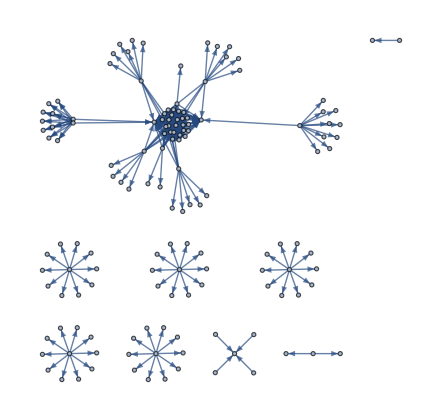

```mathematica
graphLove = Thread /@(#->WordData["love",#]&/@WordData["love","Properties"])//Flatten//Graph[#,VertexLabels->generateLabels@#]&
```

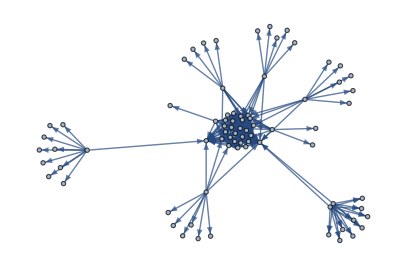
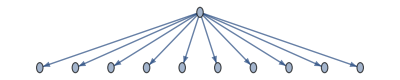
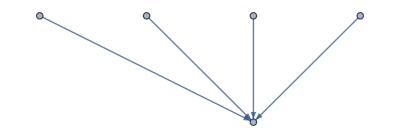
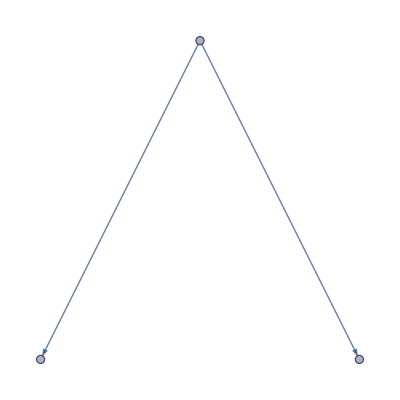
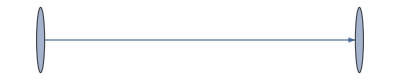
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
graphLove// WeaklyConnectedGraphComponents
```

```mathematica
ConnectedComponents[-Graphics-]
```

{{Verb},{Noun},{PartsOfSpeech}}

```mathematica
{VertexCount@graphLove,EdgeCount@graphLove}
```

{143,317}

Very rich and careful curated, a simple “love” word return a graph with 317 edges and 143 vertexes. Linguistic data from Wolfram is more than a rich dictionary

exploratory

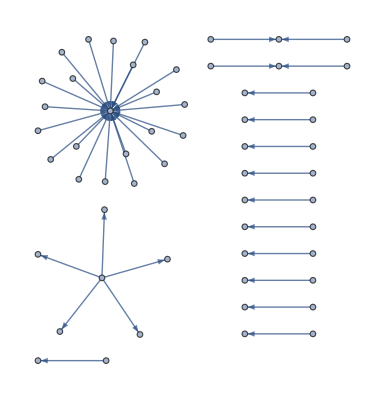

```mathematica
randomWord = RandomWord[1][[1]]
Thread /@(#->WordData[randomWord,#]&/@WordData[randomWord,"Properties"])//Flatten//Graph[#,VertexLabels->generateLabels@#]&
```

## Scratchpad

```mathematica
({"telecommuting","Noun"}->{} )//Last
```

{}

```mathematica
TypeOf[123]
```

TypeSpecifier[Integer64]

```mathematica
WordData["telecommuting","BaseForm"]
```

{$Failed}

```mathematica
WordData["telecommuting","PorterStem"]
```

telecommut

```mathematica
WordData["telecommuting","PhoneticForm"]
```

teluhkuhmy'ooting

```mathematica
WordData["telecommuting","InflectedForms"]
```

{{telecommuting,Noun}→{telecommutings}}

```mathematica
EntityPrefetch["Word"]
```

```mathematica
WordData["telecommuting","BaseForm"]
```

{$Failed}

```mathematica
WordData[All,"Preload"]
```

True

```mathematica
PacletDataRebuild[]
```

```mathematica
Entity["Word",#]&/@ RandomWord[2] //AbsoluteTiming
```

{0.017011,{bowdlerize,escapement}}

```mathematica
#["BaseForm"]&/@ {Entity["Word","bowdlerize"],Entity["Word","escapement"]}//AbsoluteTiming
```

{4.14233,{{{bowdlerize,Verb}},{{escapement,Noun}}}}

```mathematica
Information[Entity["Word","escapement"]]
```

Entity
escapement | Word

Full Dataset...

```mathematica
Entity["Word","crosshatch"][]
```

crosshatch

```mathematica
Entity["Word","crosshatch"]["BaseForm"]
```

{{crosshatch,Noun},{crosshatch,Verb}}

```mathematica
findAvailablePropertiesOfWord @"telecommuting"
```

First::normal: Nonatomic expression expected at position 1 in First[$Failed].

{BroaderTerms→{employment,work}}

```mathematica
WordData["credential","Synonyms"]
```

{{credential,Noun}→{certificate,certification,credentials}}

```mathematica
SetDirectory["~/nhannht-projects/nature"];
```

```mathematica
NotebookSave[EvaluationNotebook[],FileNameJoin[{Directory[],"humanlanguage.nb"}]]
```

```mathematica
VerminExportKeepSyntaxHighLight[]
```

```mathematica
Export[FileNameJoin[{Directory[],"humanlanguage.pdf"}],EvaluationNotebook[]]
```

/home/vermin/nhannht-projects/nature/humanlanguage.pdf